```mathematica
(*The dispersion relation*)
$Assumptions->{v≥0,0≤u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
params={(*ϵ->-x,Subscript[ϵ, l]->-x,g->√u*)ϵ->1-v/(1-u),Subscript[ϵ, l]->1-v,g->(v √u)/(1-u),Subscript[n, y]->Cos[θ]Sin[η],Subscript[n, z]->Sin[θ]};
Ο=(Ν/.disp⟦1⟧)/.params//Simplify;
X=(Ν/.disp⟦2⟧)/.params//Simplify;
Clear[a,b,c,disp,params]
```

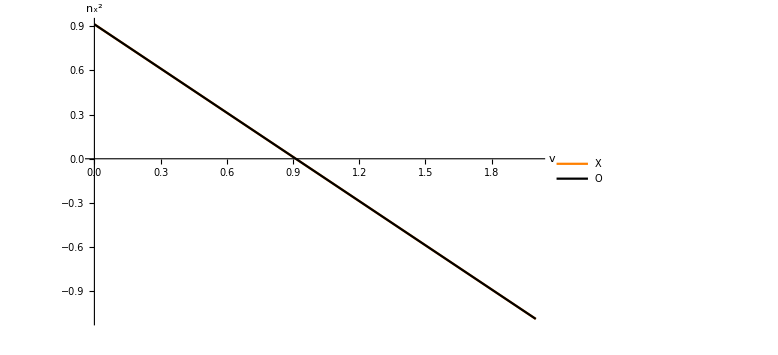

```mathematica
(*η=0*)
params={u->0,θ->0.3,η->0};
Plot[{X/.params,Ο/.params},{v,0,2},PlotStyle->{Orange,Black},PlotRange->{All,Automatic},PlotLegends->Placed[{"X","O"},Scaled[{0.7,0.7}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/isotropism.png",%,"PNG"]*)
Clear[params];
```

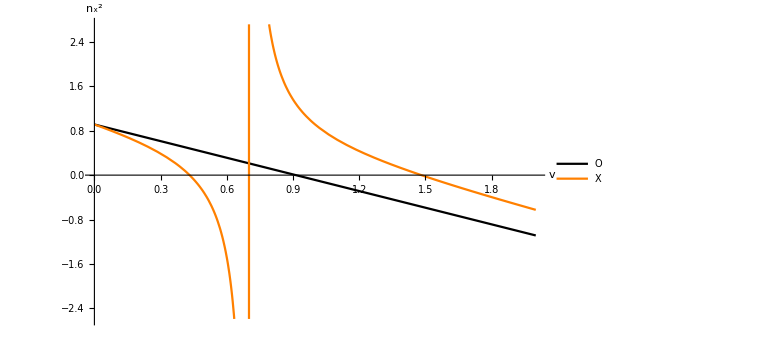

```mathematica
(*η=0*)
params={u->0.3,θ->0.3,η->0};
Plot[{Ο/.params,X/.params},{v,0,2},PlotStyle->{Black,Orange},PlotRange->{All,Automatic},PlotLegends->Placed[{"Ο","X"},Scaled[{0.7,0.7}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/eta.png",%,"PNG"]*)
Clear[params];
```

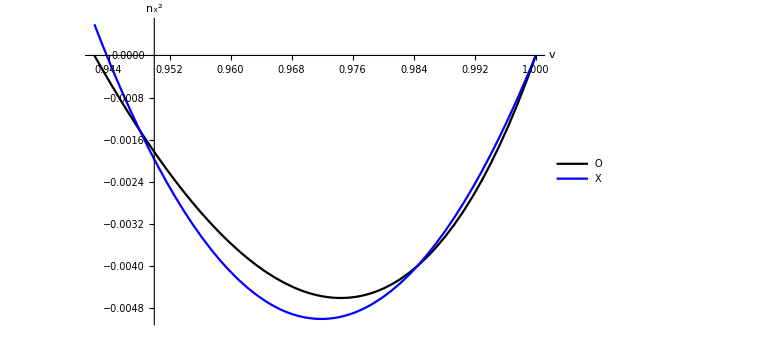

-0.005

```mathematica
(*θ=0*)
params={u->υ,ξ->ζ,θ->0,η->(ArcSin[√((√υ)/(1+√υ))]+ζ)}/.{υ->0.1,ζ->0.05};
Plot[{Ο/.params,(*X/.params,*)(2/(√u))(v-1)(v-1+2 u^(1/4)ξ)/.params},{v,Min[1,(1+√u)(1-Sin[η]^2)]/.params,Max[1,(1+√u)(1-Sin[η]^2)]/.params},PlotStyle->{Black,(*Orange,*)Blue},(*PlotRange->{All,{-2,2}},*)PlotLegends->Placed[{"Ο","X"},Scaled[{0.9,0.8}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/teta.png",%,"PNG"]*)
-2 ξ^2/.params
Clear[params];
```

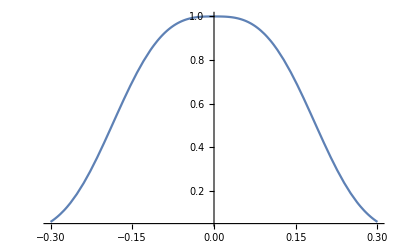

```mathematica
Plot[ⅇ^(-4χ u^(1/4) Abs[ϕ]^3)/.{χ->30,u->0.6},{ϕ,-0.3,0.3},PlotRange->Full]
```

```mathematica
$Assumptions->{v≥0,0≤u<1};
a=ϵ;
b=(g^2-ϵ^2+2 ϵ Subscript[n, z]^2-ϵ Subscript[ϵ, l]+Subscript[n, y]^2 (ϵ+Subscript[ϵ, l]));
c=ϵ Subscript[n, z]^4+(Subscript[n, y]^4-2 ϵ Subscript[n, y]^2-g^2+ϵ^2) Subscript[ϵ, l]+Subscript[n, z]^2 (g^2+(Subscript[n, y]^2 -ϵ)(ϵ+Subscript[ϵ, l]));
disp={{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2+√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2},{Ν->((ϵ-Subscript[n, y]^2 )(ϵ+Subscript[ϵ, l])-g^2-√(Subscript[n, y]^4 (ϵ-Subscript[ϵ, l])^2+(g^2-ϵ^2+ϵ Subscript[ϵ, l])^2+2 Subscript[n, y]^2 (g^2(ϵ+Subscript[ϵ, l])-ϵ(ϵ-Subscript[ϵ, l])^2)))/(2 ϵ)-Subscript[n, z]^2}};(*Ν=Subscript[n, x]^2*)
params={ϵ->1-(1+x)/(1-u),Subscript[ϵ, l]->-x,g->((1+x)√u)/(1-u),Subscript[n, y]->Sin[η],Subscript[n, z]->0};
Ο=(Ν/.disp⟦1⟧)/.params//Simplify;
X=(Ν/.disp⟦2⟧)/.params//Simplify;
Clear[a,b,c,disp,params]
```

```mathematica
(*θ=0*)
params={u->υ,η->1.3ArcSin[√((√υ)/(1+√υ))]}/.υ->0.5;
Plot[{Ο/.params,X/.params},{x,-1,2},PlotStyle->{Black,Orange},PlotRange->{All,{-2,2}},PlotLegends->Placed[{"Ο","X"},Scaled[{0.9,0.8}]],ImageSize->Large,AxesLabel->{v,Subscript[n, x]^2},LabelStyle->{FontSize->20}]
(*SaveData["results/dispersionRelations/teta.png",%,"PNG"]*)
Clear[params];
```

-Graphics-

```mathematica
Assuming[0<u<1,Simplify[Normal[Series[Ο/.Sin[η]->,{x,0,2},{ξ,0,1}]]]]
```

(2 x (x+√u ξ+3 x ξ+2 √u x ξ))/(√u)

```mathematica
Ο/.θ->0
```

-(2-2 u-4 v+u v+2 v^2-(2+u (-2+v)-2 v) Sin[η]^2+√((u v^2 (u-2 (-2+u+2 v) Sin[η]^2+u Sin[η]^4))/(-1+u)^2)-u √((u v^2 (u-2 (-2+u+2 v) Sin[η]^2+u Sin[η]^4))/(-1+u)^2))/(2 (-1+u+v))

```mathematica
-(2-2 u-4 v+u v+2 v^2-(2+u (-2+v)-2 v) Sin[η]^2+√(u v^2 (u-2 (-2+u+2 v) Sin[η]^2+u Sin[η]^4)))/(2 (-1+u+v))
```

```mathematica
Assuming[0<u<1,Integrate[√(-(2-2 u-4 v+u v+2 v^2-(2+u (-2+v)-2 v) Sin[η]^2+√(u v^2 (u-2 (-2+u+2 v) Sin[η]^2+u Sin[η]^4)))/(2 (-1+u+v))),{v,0,(1-√u)(1-Sin[η]^2)}]]
```

$Aborted

```mathematica
Assuming[v>0&&0<u<1,Solve[D[-(2-2 u-4 v+u v+2 v^2-(2+u (-2+v)-2 v) Sin[η]^2+√(u v^2 (u-2 (-2+u+2 v) Sin[η]^2+u Sin[η]^4)))/(2 (-1+u+v)),v]==0,v]]
```

$Aborted

0.059582

```mathematica
Assuming[0<u<1,Simplify[(-Ο)/.{θ->0,v->1/2(1+(1+√u)(1-Sin[η]^2))}/.Sin[η]->√((√u)/(1+√u)(1+ξ))]];
Normal[Series[%,{ξ,0,2}]]
```

(√u ξ^2)/2

{u→0.3,θ→0,η→0.673751}

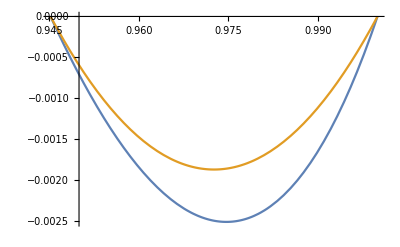

```mathematica
params={u->υ,θ->0,η->ArcSin[√((√υ)/(1+√υ)(1+ξ))]}/.{υ->0.3,ξ->0.1}
Plot[{Ο/.params,(*X/.params,*)2.5(v-1)(v-(1+√u)(1-Sin[η]^2))/.params},{v,Min[1,(1+√u)(1-Sin[η]^2)]/.params,Max[1,(1+√u)(1-Sin[η]^2)]/.params}]
```

```mathematica
Ο/.params
```

-(1.4-0.353889 (2+0.3 (-2+v)-2 v)-3.7 v+2 v^2+0.547723 √(v^2 (0.337571-0.707779 (-1.7+2 v))))/(2 (-0.7+v))

```mathematica
Min[1,(1+√u)(1-Sin[η]^2)]/.params
```

1

```mathematica
Max[1,(1+√u)(1-Sin[η]^2)]/.params
```

1.

```mathematica
-(√u (-1-2 √u+2 u^(3/2)+ u^2) ξ^2)/(2(-1+√u) (1+√u)^3)//Simplify
```

-1/2 √u ξ^2

```mathematica
(x-a)(x-b);
%/.Solve[D[%,x]==0,x]⟦1⟧//Simplify
```

-1/4 (a-b)^2

```mathematica
Series[(1+√u)(1-Sin[η]^2)/.η->ArcSin[√((√u)/(1+√u)(1+ζ))],{ζ,0,4}]
```

1-√u ζ+O[ζ]^5

```mathematica
Assuming[a>0,Integrate[√(x(x-a)),{x,0,a}]]
```

1/8 ⅈ a^2 π